```mathematica
line[x_, a_, m_]:= Piecewise[{{-(m-a)/a Abs[x]+m-a, -(m-a)/a Abs[x]+m-a> 0}, {0, True}}];
```

Plot::plln: Limiting value -c in {x,-c,c} is not a machine-sized real number.

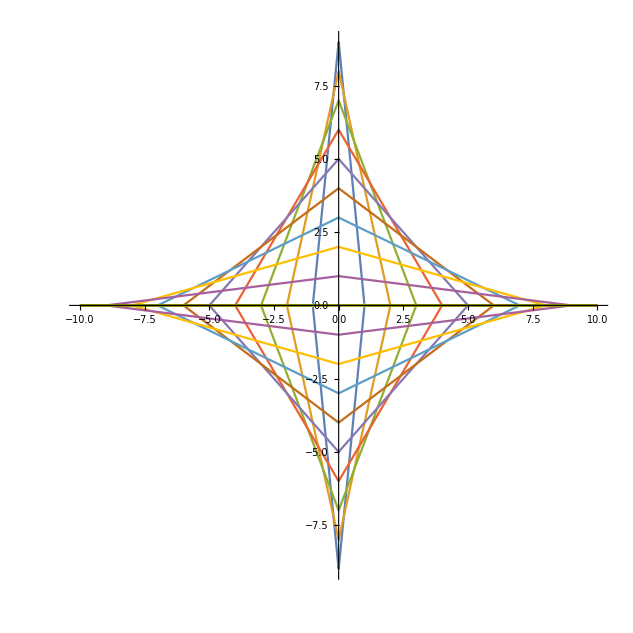

```mathematica
Plot[Table[{line[x,a,c], -line[x,a,c]}//Flatten, {a, 1,c}], {x, -c, c}, {AspectRatio->1,PlotRange->Full, Evaluated->True}]/.c-> 10
```